# DescendingSublists

DescendingSublists[list]
makes sublists of list starting at its left-to-right maxima.

The elements in the sublists are in the same order as the original list.

A left-to-right maximum is greater than any preceding element.

The first element of each sublist is its maximum.

The first elements of the sublists are increasing.

## See AlsoSeeAlsoInsert links to any related reference (function) pages.

Cycles ▪ PermutationList ▪

## Tech NotesTechNotesInsert links to related tech notes.

## Related Guides

## Related LinksRelatedLinksInsert links to any related page, including web pages.

## Examples InitializationExamplesInitializationInput that is to be evaluated before any examples are run, e.g. Needs[…].

```mathematica
Needs["PeterBurbery`Combinatorics`"]
```

## Basic Examples | More Examples ⊳

Split a permutation given as a list into sublists starting at its left-to-right maximum:

```mathematica
DescendingSublists@{2,4,1,6,7,5,3}
```

{{2},{4,1},{6},{7,5,3}}

The input does not have to be a permutation:

```mathematica
r1=RandomInteger[{1,7},20]
```

{2,7,3,2,7,7,2,2,2,6,1,6,3,5,2,4,6,2,5,5}

```mathematica
DescendingSublists@r1
```

{{2},{7,3,2,7,7,2,2,2,6,1,6,3,5,2,4,6,2,5,5}}

Flatten to get back the original list:

```mathematica
r1==Flatten@%
```

True

## More ExamplesMoreExamplesExtended examples in standardized sections.

### Scope

Here is a larger example:

```mathematica
p1=PermutationList@RandomPermutation@50
```

{33,28,49,14,17,4,15,27,24,31,46,43,40,10,9,36,29,34,13,11,12,16,5,25,3,8,44,21,23,1,39,20,22,35,48,26,19,45,7,37,50,38,30,41,42,2,32,18,6,47}

```mathematica
s1=DescendingSublists@p1
```

{{33,28},{49,14,17,4,15,27,24,31,46,43,40,10,9,36,29,34,13,11,12,16,5,25,3,8,44,21,23,1,39,20,22,35,48,26,19,45,7,37},{50,38,30,41,42,2,32,18,6,47}}

Each sublist starts from its maximum:

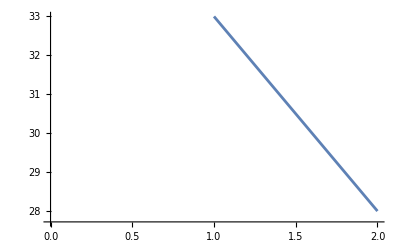
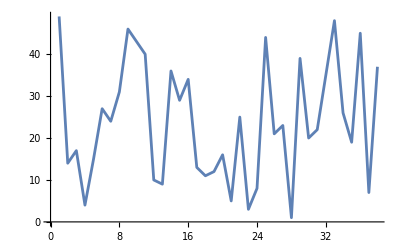
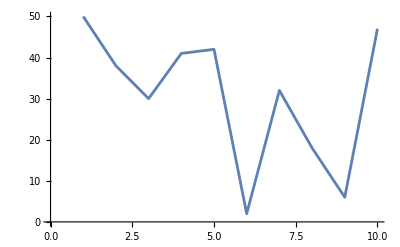

```mathematica
Row[ListLinePlot/@s1]
```

The first elements are increasing:

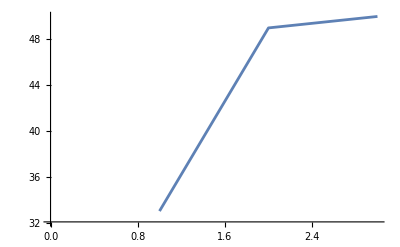

```mathematica
ListLinePlot[First/@s1]
```

The sublists of s1 an be thought of as cycle notation for the permutation, but with a different canonical form than the Wolfram Language default, where each sublist starts with its minimum:

```mathematica
Cycles[s1]
```

Cycles[{{1,39,20,22,35,48,26,19,45,7,37,49,14,17,4,15,27,24,31,46,43,40,10,9,36,29,34,13,11,12,16,5,25,3,8,44,21,23},{2,32,18,6,47,50,38,30,41,42},{28,33}}]

### Generalizations & Extensions

### Options

### Applications

### Properties & Relations

### Possible Issues

### Interactive Examples

### Neat Examples

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Symbol

PeterBurbery/Combinatorics

PeterBurbery`Combinatorics`

PeterBurbery/Combinatorics/ref/DescendingSublists

### Keywords

### Syntax Templates